0) Preliminaries

```mathematica
plotFun[fun_,lims_,epilog_,label_]:=Framed@Plot[fun,{x,lims[[1,1]],lims[[1,2]]},PlotRange->{All,{lims[[2,1]],lims[[2,2]]}},Epilog->epilog,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"x","y"},BaseStyle->{FontSize->20}]
```

```mathematica
discPlotFun[fun_,range_,lims_,epilog_,label_]:=Framed@DiscretePlot[fun,{x,range[[1]],range[[2]]},PlotRange->lims,Epilog->epilog,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"j","y"},BaseStyle->{FontSize->20}]
```

1) Sketch plots of functions

## Function 1

f: ℝ\{-1} → ℝ	
x↦1/(1+x)

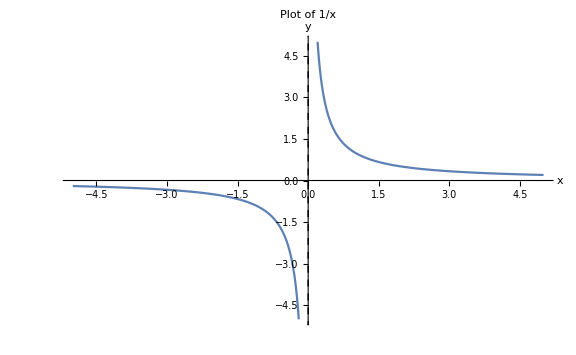

```mathematica
plotFun[1/x,{{-5,5},{-5,5}},{Dashed,InfiniteLine[{0,1},{0,1}]},"Plot of 1/x"]
```

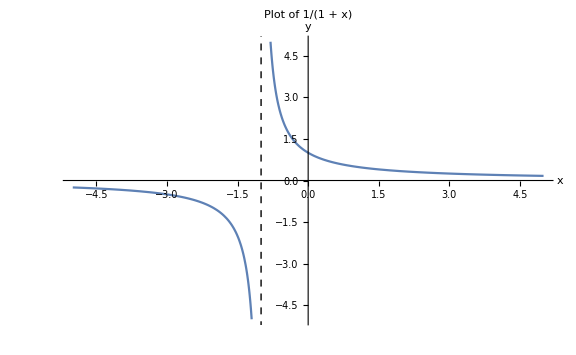

```mathematica
plotFun[1/(1+x),{{-5,5},{-5,5}},{Dashed,InfiniteLine[{-1,1},{0,1}]},"Plot of 1/(1 + x)"]
```

No x value maps to y = 0, so the function is not surjective.

## Function 2

f: ℝ → ℝ	
x↦|x^2-1|

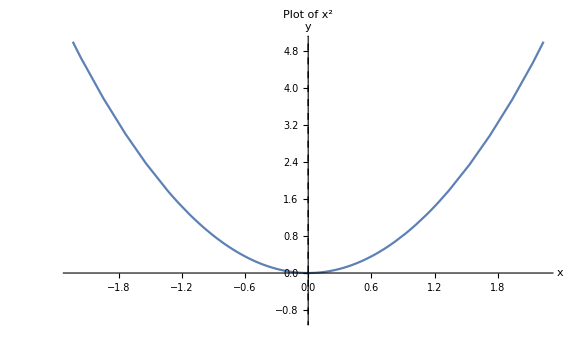

```mathematica
plotFun[x^2,{{-5,5},{-1,5}},{Dashed,InfiniteLine[{0,1},{0,1}]},"Plot of x^2"]
```

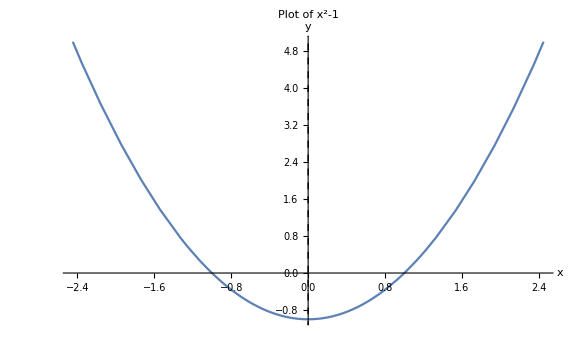

```mathematica
plotFun[x^2-1,{{-5,5},{-1,5}},{Dashed,InfiniteLine[{0,1},{0,1}]},"Plot of x^2-1"]
```

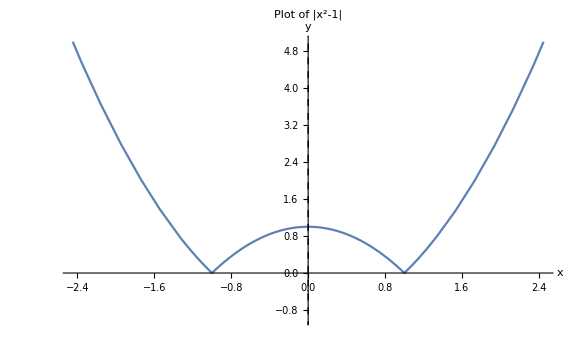

```mathematica
plotFun[Abs[x^2-1],{{-5,5},{-1,5}},{Dashed,InfiniteLine[{0,1},{0,1}]},"Plot of |x^2-1|"]
```

No x value maps to negative values of y, so the function is not surjective.

2) Bijective, surjective, injective functions

## Function 1

f: ℝ → ℝ	
f(x)=x^2

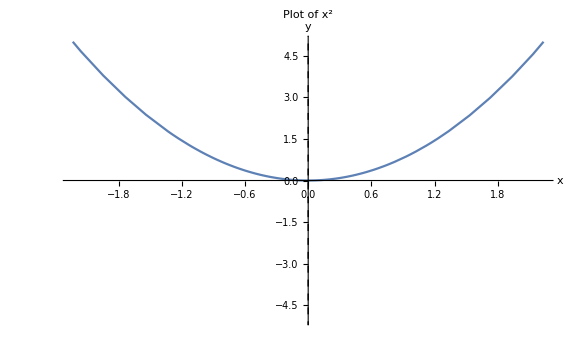

```mathematica
plotFun[x^2,{{-5,5},{-5,5}},{Dashed,InfiniteLine[{0,1},{0,1}]},"Plot of x^2"]
```

Not surjective, not injective, not bijective.

## Function 2

f: ℝ → ℝ	
f(x)=x^3

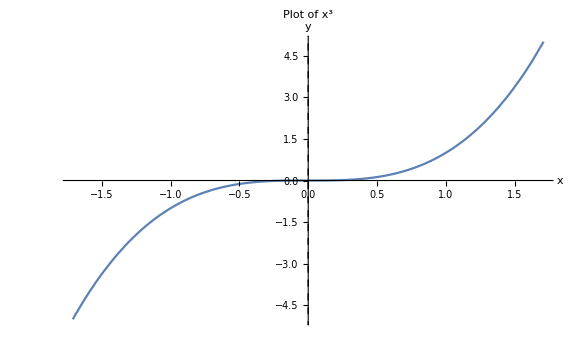

```mathematica
plotFun[x^3,{{-5,5},{-5,5}},{Dashed,InfiniteLine[{0,1},{0,1}]},"Plot of x^3"]
```

Is both surjective and injective, and thus also bijective.

## Function 3

f: {1,2,3} → {0,1,2,3}	
f(j)=j-1

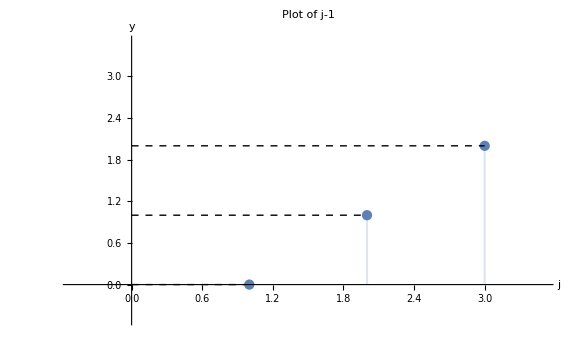

```mathematica
discPlotFun[x-1,{1,3},{{-0.5,3.5},{-0.5,3.5}},{Dashed,Line[{{{0,0},{1,0}},{{0,1},{2,1}},{{0,2},{3,2}}}]},"Plot of j-1"]
```

Is injective, but not surjective, and thus not bijective.

3) Union of intervals

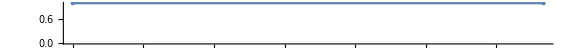

```mathematica
Framed@NumberLinePlot[Interval[{0,1}],ImageSize->Large]
```

For the rest see the exercise class...

4) Images of subsets

f: A→B
E, F ⊂ B

f^-1(E ∪ F) =f^-1(E) ∪ f^-1(F)

For the rest see the exercise class...

5) Summation

Axioms:

Associativity of addition

∀x,y,z∈𝕂: (x+y)+z = x+(y+z)

Commutativity of addition

∀x,y∈𝕂: x+y= y+x

Commutativity of multiplication

∀x,y∈𝕂: x·y= y·x

Distributivity

∀x,y,z∈𝕂: (x+y)·z = x·z+y·z

Proof by mathematical induction...

```mathematica
(∑_(k=1)^n Subscript[a, k]) (∑_(l=1)^m Subscript[b, l])==∑_(k=1)^n ∑_(l=1)^m Subscript[a, k] Subscript[b, l]
```

6) Cartesian products

## Case 1

A = [0,1]
B = ℝ^+

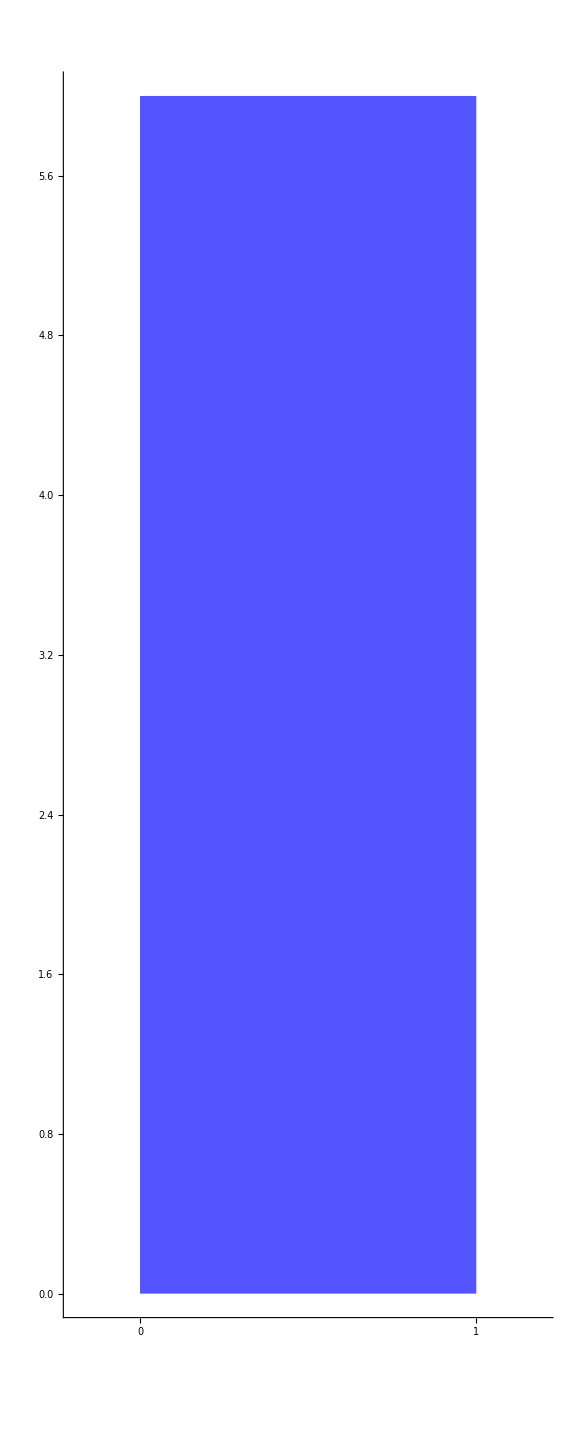

```mathematica
Graphics[{Lighter[Blue],Rectangle[{1,0},{2,6}]},Axes->True,Ticks->{{{1,0},{2,1}},Automatic},BaseStyle->{FontSize->20},PlotRange->{{0.8,2.2},All},ImageSize->Large]
```

## Case 2

A = {0,1}
B = [-1,1]

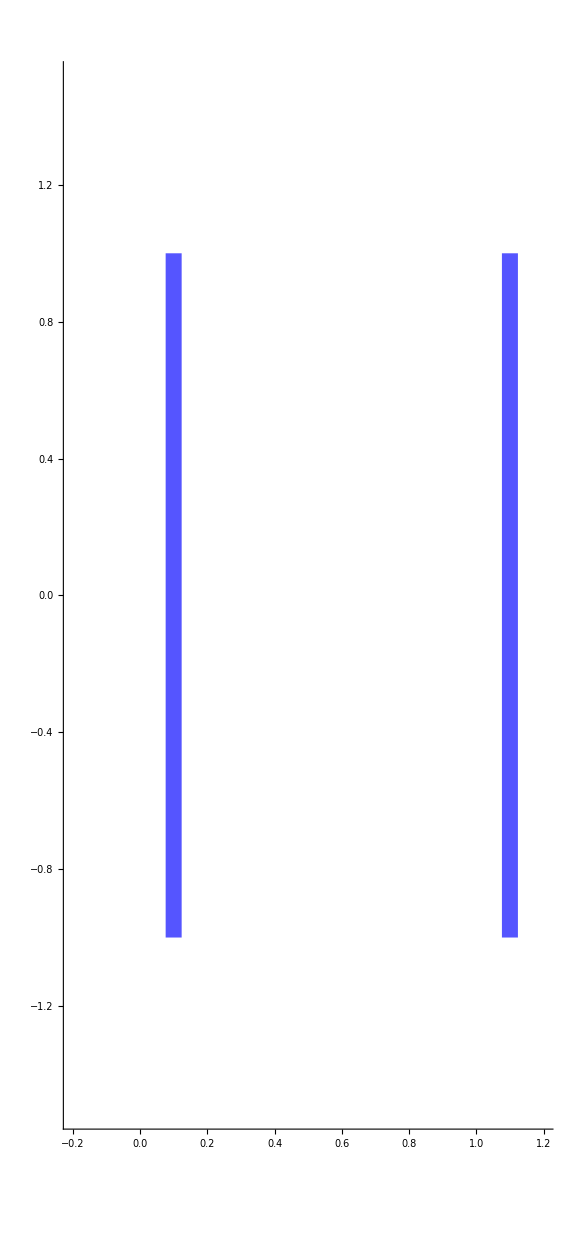

```mathematica
dx=.1;
Graphics[{Lighter[Blue],Thickness[.02],Line[{{{dx,-1},{dx,1}},{{dx+1,-1},{dx+1,1}}}]},Axes->True,(*Ticks->{{{dx,0},{dx+1,1}},Automatic},*)BaseStyle->{FontSize->20},PlotRange->{{-0.2,1.2},{-1.5,1.5}},ImageSize->Large]
```